## First experiments

```mathematica
Table[
Table[PartitionHasPattern[p8,p7]
,{p7,QuadrilateralsWithPattern[7,1]}]//Tally//Sort
,{p8,QuadrilateralsWithPattern[8,1]}
]//Tally//Sort
```

{{{{False,15},{True,1}},64}}

```mathematica
Table[
Table[PartitionHasPattern[p8,p7]
,{p8,QuadrilateralsWithPattern[8,1]}]//Tally//Sort
,{p7,QuadrilateralsWithPattern[7,1]}
]//Tally//Sort
```

{{{{False,60},{True,4}},16}}

```mathematica
Table[
p7->
Sort[Select[QuadrilateralsWithPattern[8,1],PartitionHasPattern[#,p7]&]]
,{p7,QuadrilateralsWithPattern[7,1]}
]//Sort
```

{{{1,3},{2},{4},{5,6,7}}→{{{1,3},{2},{4},{5,6,7,8}},{{1,3},{2},{4,8},{5,6,7}},{{1,3},{2,8},{4},{5,6,7}},{{1,3,8},{2},{4},{5,6,7}}},{{1,3},{2},{4,6},{5,7}}→{{{1,3},{2},{4,6},{5,7,8}},{{1,3},{2},{4,6,8},{5,7}},{{1,3},{2,8},{4,6},{5,7}},{{1,3,8},{2},{4,6},{5,7}}},{{1,3},{2},{4,7},{5,6}}→{{{1,3},{2},{4,7},{5,6,8}},{{1,3},{2},{4,7,8},{5,6}},{{1,3},{2,8},{4,7},{5,6}},{{1,3,8},{2},{4,7},{5,6}}},{{1,3},{2},{4,6,7},{5}}→{{{1,3},{2},{4,6,7},{5,8}},{{1,3},{2},{4,6,7,8},{5}},{{1,3},{2,8},{4,6,7},{5}},{{1,3,8},{2},{4,6,7},{5}}},{{1,3},{2,6},{4},{5,7}}→{{{1,3},{2,6},{4},{5,7,8}},{{1,3},{2,6},{4,8},{5,7}},{{1,3},{2,6,8},{4},{5,7}},{{1,3,8},{2,6},{4},{5,7}}},{{1,3},{2,6},{4,7},{5}}→{{{1,3},{2,6},{4,7},{5,8}},{{1,3},{2,6},{4,7,8},{5}},{{1,3},{2,6,8},{4,7},{5}},{{1,3,8},{2,6},{4,7},{5}}},{{1,3},{2,7},{4},{5,6}}→{{{1,3},{2,7},{4},{5,6,8}},{{1,3},{2,7},{4,8},{5,6}},{{1,3},{2,7,8},{4},{5,6}},{{1,3,8},{2,7},{4},{5,6}}},{{1,3},{2,7},{4,6},{5}}→{{{1,3},{2,7},{4,6},{5,8}},{{1,3},{2,7},{4,6,8},{5}},{{1,3},{2,7,8},{4,6},{5}},{{1,3,8},{2,7},{4,6},{5}}},{{1,3},{2,6,7},{4},{5}}→{{{1,3},{2,6,7},{4},{5,8}},{{1,3},{2,6,7},{4,8},{5}},{{1,3},{2,6,7,8},{4},{5}},{{1,3,8},{2,6,7},{4},{5}}},{{1,3,6},{2},{4},{5,7}}→{{{1,3,6},{2},{4},{5,7,8}},{{1,3,6},{2},{4,8},{5,7}},{{1,3,6},{2,8},{4},{5,7}},{{1,3,6,8},{2},{4},{5,7}}},{{1,3,6},{2},{4,7},{5}}→{{{1,3,6},{2},{4,7},{5,8}},{{1,3,6},{2},{4,7,8},{5}},{{1,3,6},{2,8},{4,7},{5}},{{1,3,6,8},{2},{4,7},{5}}},{{1,3,6},{2,7},{4},{5}}→{{{1,3,6},{2,7},{4},{5,8}},{{1,3,6},{2,7},{4,8},{5}},{{1,3,6},{2,7,8},{4},{5}},{{1,3,6,8},{2,7},{4},{5}}},{{1,3,7},{2},{4},{5,6}}→{{{1,3,7},{2},{4},{5,6,8}},{{1,3,7},{2},{4,8},{5,6}},{{1,3,7},{2,8},{4},{5,6}},{{1,3,7,8},{2},{4},{5,6}}},{{1,3,7},{2},{4,6},{5}}→{{{1,3,7},{2},{4,6},{5,8}},{{1,3,7},{2},{4,6,8},{5}},{{1,3,7},{2,8},{4,6},{5}},{{1,3,7,8},{2},{4,6},{5}}},{{1,3,7},{2,6},{4},{5}}→{{{1,3,7},{2,6},{4},{5,8}},{{1,3,7},{2,6},{4,8},{5}},{{1,3,7},{2,6,8},{4},{5}},{{1,3,7,8},{2,6},{4},{5}}},{{1,3,6,7},{2},{4},{5}}→{{{1,3,6,7},{2},{4},{5,8}},{{1,3,6,7},{2},{4,8},{5}},{{1,3,6,7},{2,8},{4},{5}},{{1,3,6,7,8},{2},{4},{5}}}}

## And now a concrete example

```mathematica
start71=First[QuadrilateralsWithPattern[7,1]];
```

```mathematica
start72=First[QuadrilateralsWithPattern[7,2]];
```

```mathematica
start73=First[QuadrilateralsWithPattern[7,3]];
```

```mathematica
start74=First[QuadrilateralsWithPattern[7,4]];
```

```mathematica
start75=First[QuadrilateralsWithPattern[7,5]];
```

```mathematica
PatternCompare[s1_,s2_]:=Block[{
simp1=SymbolToSets[s1],
simp2=SymbolToSets[s2]
},
simp1=Select[Map[Intersection[#,{1,2,3,4,5}]&,simp1],#≠{}&];
simp2=Select[Map[Intersection[#,{1,2,3,4,5}]&,simp2],#≠{}&];
Return[CompareSymbols[SetsToSymbol2[simp1],SetsToSymbol2[simp2]]]
]
```

```mathematica
ShowGraphForParts[part1_,part2_,part3_,part4_,part5_]:=Block[
{
e1=EdgeList[GraphComplement[GraphFromSets[part1]]],
e2=EdgeList[GraphComplement[GraphFromSets[part2]]],
e3=EdgeList[GraphComplement[GraphFromSets[part3]]],
e4=EdgeList[GraphComplement[GraphFromSets[part4]]],
e5=EdgeList[GraphComplement[GraphFromSets[part5]]],
nodes=Length[Flatten[part1]]
},
{Select[Sort[FindFullFormula[ EdgeDelete[CompleteGraph[nodes],DeleteDuplicates[Join[e1,e2,e3,e4,e5]]]],PatternCompare], SymbolLevel[#]==4&],{part1,part2,part3,part4,part5}}
]
```

```mathematica
ShowSol[sol_]:=Block[
{
start = Select[sol[[1]],MemberQ[sol[[2]],SymbolToSets[#]]&],
other = Select[sol[[1]],!MemberQ[sol[[2]],SymbolToSets[#]]&]
},
ShowGraphs[start,Directive[Dotted,Thick,Orange]&]->
ShowGraphs[other,If[HasQuadrilateralPattern[#],Red,Darker[Green]]&]
]
```

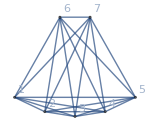
{-Graphics-13♁26♁47,-Graphics-14♁26♁37,-Graphics-16♁24♁37,-Graphics-16♁25♁37,-Graphics-16♁27♁35}→{-Graphics-16♁247,-Graphics-16♁25♁47,-Graphics-26♁35♁47,-Graphics-16♁35♁47,-Graphics-13♁247,-Graphics-13♁25♁47,-Graphics-14♁25♁37,-Graphics-14♁27♁35,-Graphics-14♁26♁35,-Graphics-247♁35,-Graphics-16♁24♁35}

```mathematica
ShowGraphForParts[start71,start72,start73,start74,start75]//ShowSol
```

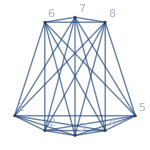
{{{{{{-Graphics-13♁26♁47♁58,-Graphics-14♁26♁37♁58,-Graphics-16♁24♁37♁58,-Graphics-16♁258♁37,-Graphics-16♁27♁358}→{-Graphics-16♁247♁58,-Graphics-16♁247♁38,-Graphics-16♁258♁47,-Graphics-16♁25♁38♁47,-Graphics-26♁358♁47,-Graphics-16♁358♁47,-Graphics-16♁28♁35♁47,-Graphics-13♁247♁58,-Graphics-13♁258♁47,-Graphics-14♁258♁37,-Graphics-14♁27♁358,-Graphics-14♁26♁358,-Graphics-247♁358,-Graphics-16♁24♁358,-Graphics-16♁247♁35}}}}}}

```mathematica
Table[
Table[
Table[
Table[
Table[
ShowSol[ShowGraphForParts[part1,part2,part3,part4,part5]]
,
{part5,Take[Sort[Select[QuadrilateralsWithPattern[8,5],PartitionHasPattern[#,start75]&]],{3,3}]}
],
{part4,Take[Sort[Select[QuadrilateralsWithPattern[8,4],PartitionHasPattern[#,start74]&]],1]}
],
{part3,Take[Sort[Select[QuadrilateralsWithPattern[8,3],PartitionHasPattern[#,start73]&]],{2,2}]}
],
{part2,Take[Sort[Select[QuadrilateralsWithPattern[8,2],PartitionHasPattern[#,start72]&]],1]}
],
{part1,Take[Sort[Select[QuadrilateralsWithPattern[8,1],PartitionHasPattern[#,start71]&]],1]}
]
```

## Now with 8

```mathematica
start81=First[QuadrilateralsWithPattern[8,1]];
```

```mathematica
start82=First[QuadrilateralsWithPattern[8,2]];
```

```mathematica
start83=First[QuadrilateralsWithPattern[8,3]];
```

```mathematica
start84=First[QuadrilateralsWithPattern[8,4]];
```

```mathematica
start85=First[QuadrilateralsWithPattern[8,5]];
```

```mathematica
ShowGraphForParts[start81,start82,start83,start84,start85]//ShowSol
```

{-Graphics-13♁26♁47♁58,-Graphics-14♁26♁37♁58,-Graphics-16♁24♁37♁58,-Graphics-16♁25♁37♁48,-Graphics-16♁27♁35♁48}→{-Graphics-16♁247♁58,-Graphics-13♁247♁58,-Graphics-16♁247♁35}

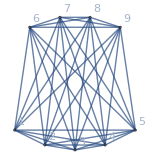
{{{{{{-Graphics-13♁26♁47♁589,-Graphics-14♁26♁37♁589,-Graphics-16♁24♁37♁589,-Graphics-16♁25♁37♁489,-Graphics-16♁27♁35♁489}→{-Graphics-16♁247♁589,-Graphics-13♁247♁589,-Graphics-16♁247♁35♁89}}}}},{{{{{-Graphics-13♁26♁479♁58,-Graphics-14♁26♁37♁589,-Graphics-16♁24♁37♁589,-Graphics-16♁25♁37♁489,-Graphics-16♁27♁35♁489}→{-Graphics-13♁26♁47♁589,-Graphics-16♁247♁589,-Graphics-13♁247♁589,-Graphics-16♁247♁35♁89}}}}},{{{{{-Graphics-13♁269♁47♁58,-Graphics-14♁26♁37♁589,-Graphics-16♁24♁37♁589,-Graphics-16♁25♁37♁489,-Graphics-16♁27♁35♁489}→{-Graphics-13♁26♁47♁589,-Graphics-14♁269♁37♁58,-Graphics-16♁247♁589,-Graphics-16♁249♁37♁58,-Graphics-16♁259♁37♁48,-Graphics-13♁247♁589,-Graphics-13♁247♁58♁69,-Graphics-16♁247♁35♁89}}}}},{{{{{-Graphics-139♁26♁47♁58,-Graphics-14♁26♁37♁589,-Graphics-16♁24♁37♁589,-Graphics-16♁25♁37♁489,-Graphics-16♁27♁35♁489}→{-Graphics-13♁26♁47♁589,-Graphics-149♁26♁37♁58,-Graphics-16♁247♁589,-Graphics-16♁247♁39♁58,-Graphics-16♁27♁359♁48,-Graphics-13♁247♁589,-Graphics-139♁247♁58,-Graphics-16♁247♁359,-Graphics-16♁247♁35♁89}}}}}}

```mathematica
Table[
Table[
Table[
Table[
Table[
ShowSol[ShowGraphForParts[part1,part2,part3,part4,part5]]
,
{part5,Take[Sort[Select[QuadrilateralsWithPattern[9,5],PartitionHasPattern[#,start85]&]],1]}
],
{part4,Take[Sort[Select[QuadrilateralsWithPattern[9,4],PartitionHasPattern[#,start84]&]],1]}
],
{part3,Take[Sort[Select[QuadrilateralsWithPattern[9,3],PartitionHasPattern[#,start83]&]],1]}
],
{part2,Take[Sort[Select[QuadrilateralsWithPattern[9,2],PartitionHasPattern[#,start82]&]],1]}
],
{part1,Take[Sort[Select[QuadrilateralsWithPattern[9,1],PartitionHasPattern[#,start81]&]],{1,4}]}
]
```

## Now with 6

```mathematica
start61=First[QuadrilateralsWithPattern[6,1]];
```

```mathematica
start62=First[QuadrilateralsWithPattern[6,2]];
```

```mathematica
start63=First[QuadrilateralsWithPattern[6,3]];
```

```mathematica
start64=First[QuadrilateralsWithPattern[6,4]];
```

```mathematica
start65=First[QuadrilateralsWithPattern[6,5]];
```

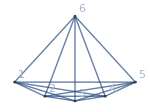
{-Graphics-13♁26,-Graphics-14♁26,-Graphics-16♁24,-Graphics-16♁25,-Graphics-16♁35}→{-Graphics-26♁35,-Graphics-13♁24,-Graphics-13♁25,-Graphics-14♁25,-Graphics-14♁35,-Graphics-24♁35}

```mathematica
ShowGraphForParts[start61,start62,start63,start64,start65]//ShowSol
```

```mathematica
Flatten[Table[
Table[
Table[
Table[
Table[
ShowSol[ShowGraphForParts[part1,part2,part3,part4,part5]]
,
{part5,Take[Sort[Select[QuadrilateralsWithPattern[7,5],PartitionHasPattern[#,start65]&]],1]}
],
{part4,Take[Sort[Select[QuadrilateralsWithPattern[7,4],PartitionHasPattern[#,start64]&]],1]}
],
{part3,Take[Sort[Select[QuadrilateralsWithPattern[7,3],PartitionHasPattern[#,start63]&]],1]}
],
{part2,Take[Sort[Select[QuadrilateralsWithPattern[7,2],PartitionHasPattern[#,start62]&]],1]}
],
{part1,Take[Sort[Select[QuadrilateralsWithPattern[7,1],PartitionHasPattern[#,start61]&]],{1,4}]}
],
5]
```

{{-Graphics-13♁26♁57,-Graphics-14♁26♁57,-Graphics-16♁24♁57,-Graphics-16♁25♁47,-Graphics-16♁35♁47}→{-Graphics-13♁26♁47,-Graphics-26♁35♁47,-Graphics-13♁24♁57,-Graphics-13♁25♁47,-Graphics-14♁26♁35,-Graphics-16♁24♁35},{-Graphics-13♁26♁47,-Graphics-14♁26♁57,-Graphics-16♁24♁57,-Graphics-16♁25♁47,-Graphics-16♁35♁47}→{-Graphics-13♁26♁57,-Graphics-26♁35♁47,-Graphics-13♁24♁57,-Graphics-13♁25♁47,-Graphics-14♁26♁35,-Graphics-16♁24♁35},{-Graphics-13♁267,-Graphics-14♁26♁57,-Graphics-16♁24♁57,-Graphics-16♁25♁47,-Graphics-16♁35♁47}→{-Graphics-13♁26♁57,-Graphics-13♁26♁47,-Graphics-14♁267,-Graphics-16♁247,-Graphics-16♁257,-Graphics-267♁35,-Graphics-26♁35♁47,-Graphics-16♁27♁35,-Graphics-13♁247,-Graphics-13♁24♁67,-Graphics-13♁24♁57,-Graphics-13♁257,-Graphics-13♁25♁67,-Graphics-13♁25♁47,-Graphics-14♁257,-Graphics-14♁25♁67,-Graphics-14♁35♁67,-Graphics-14♁27♁35,-Graphics-14♁26♁35,-Graphics-247♁35,-Graphics-24♁35♁67,-Graphics-16♁24♁35},{-Graphics-137♁26,-Graphics-14♁26♁57,-Graphics-16♁24♁57,-Graphics-16♁25♁47,-Graphics-16♁35♁47}→{-Graphics-13♁26♁57,-Graphics-13♁26♁47,-Graphics-147♁26,-Graphics-14♁26♁37,-Graphics-16♁24♁37,-Graphics-16♁25♁37,-Graphics-26♁357,-Graphics-26♁35♁47,-Graphics-17♁26♁35,-Graphics-16♁357,-Graphics-137♁24,-Graphics-13♁24♁57,-Graphics-137♁25,-Graphics-13♁25♁47,-Graphics-147♁25,-Graphics-14♁25♁37,-Graphics-14♁357,-Graphics-147♁35,-Graphics-14♁26♁35,-Graphics-24♁357,-Graphics-17♁24♁35,-Graphics-16♁24♁35}}